## Solution for ellipsoidal Heat Sources in Dimensionless Form

```mathematica
Clear[v,x,κ,y,z,t,ts,v,n]
```

Define the dimensionless coordinates:

```mathematica
ξ = v x /(2 κ); ψ = v y / (2 κ); ζ = v z / (2 κ);
```

Dimensional Time:

```mathematica
τ = v^2(t-ts)/(2κ);
```

```mathematica
Clear[θ,τ]
```

Dimensionless heat source parameters:

```mathematica
Subscript[u, a]=v Subscript[a, h]/ (2 κ √6); Subscript[u, b]=v Subscript[b, h]/(2 κ √6); Subscript[u, c]=v Subscript[c, h]/(2 κ √6)
```

(v c_h)/(2 √6 κ)

Christensen parameter:

```mathematica
n = PL v / (4 π κ^2 ρ c (Tm-T0)); A1 = Exp[-(ξ + τ)^2/(2(τ+Subscript[u, c]^2))-(ψ)^2/(2(τ+Subscript[u, a]^2))-(ζ )^2/(2(τ+Subscript[u, b]^2))];
```

```mathematica
A1
```

ⅇ^(-(v^2 y^2)/(8 κ^2 (((t-ts) v^2)/(2 κ)+(v^2 a_h^2)/(24 κ^2)))-(v^2 z^2)/(8 κ^2 (((t-ts) v^2)/(2 κ)+(v^2 b_h^2)/(24 κ^2)))-((((t-ts) v^2)/(2 κ)+(v x)/(2 κ))^2)/(2 (((t-ts) v^2)/(2 κ)+(v^2 c_h^2)/(24 κ^2))))

Result in the dimensionless form is given as:

```mathematica
θ = 1/(√2π)Integrate[1/(√(τ+Subscript[u, a]^2)√(τ+Subscript[u, b]^2))(A1/(√(τ+Subscript[u, c]^2))),{τ,0,τmax}]n
```

$Aborted

Material parameters for the elliptical heat source:

```mathematica
ρ = 4450; (*density in kg/m^3*)
cp = 546; (* specific heat in J/kg K *)
k = 6; (* conductivity W/m K *)
a = 0.000075;  (*laser dimensions*)
c =3*a;
b = 0.00005; 
n[P_,ρ_, cp_, ah_, bh_, ch_,Tm_,To_,v_]:= P v/(4 π κ^2 ρ cp (Tm - To))
```

SetDelayed::write: Tag Times in (0.0794781 PL v)/((-T0+Tm) κ^2)[P_,ρ_,cp_,ah_,bh_,ch_,Tm_,To_,v_] is Protected.

$Failed

Equation for the maximum of the heat:

```mathematica
Qmax[x_,y_,Q_,a_,b_,c_,d_,l_,B_] := (24 Q √3)/(π √π a b c Erf[(d √3)/c](Erf[((l-x)√3)/c]+Erf[((l+x)√3)/c])(Erf[((B-y)√3)/a]+Erf[((B+y)√3)/a]));
```

```mathematica
Qmax[0.2,0.3,10000,0.04,0.05,0.02,0.1,0.2,0.4]
```

9.33162×10^8

Effective heat:

```mathematica
Qeff[xs_,ys_,zs_]:= Qmax * Exp[-3 xs^2/c^2-3 ys^2/a^2-3 zs^2/b^2]
```

The full solution is given as:
T (x, y, z, t) -  T_o= ∫Qdt'/ρc[4πκ(t-t')]^(3/2)I_L I_D I_B where the integrals are defined as 
I_L=∫exp(-3 x'^2/c^2-(x-x')^2/(4κ(t-t')))dx'

```mathematica
Integrate[Exp[-3 xs^2/c^2-(x-xs)^2/(4a(t-ts))],{xs,-L-x,L-x}]
```

(0.886227 ⅇ^(((2.77556×10^-17-3333.33 t+3333.33 ts) x^2)/((t-1. ts) (0.00005625+1. t-1. ts))) √(-1. t+1. ts) (1. Erfi[((3333.33+5.92593×10^7 t-5.92593×10^7 ts) (L-x)-3333.33 x)/(√(3333.33+5.92593×10^7 t-5.92593×10^7 ts) √(-1. t+1. ts))]-1. Erfi[(-3333.33 x-5.92593×10^7 (0.00005625+1. t-1. ts) (L+x))/(√(3333.33+5.92593×10^7 t-5.92593×10^7 ts) √(-1. t+1. ts))]))/(√(3333.33+5.92593×10^7 t-5.92593×10^7 ts))

```mathematica
% // Simplify
```

(0.886227 ⅇ^(((2.77556×10^-17-3333.33 t+3333.33 ts) x^2)/((t-1. ts) (0.00005625+1. t-1. ts))) √(-1. t+1. ts) (1. Erfi[((3333.33+5.92593×10^7 t-5.92593×10^7 ts) (L-x)-3333.33 x)/(√(3333.33+5.92593×10^7 t-5.92593×10^7 ts) √(-1. t+1. ts))]-1. Erfi[(-3333.33 x-5.92593×10^7 (0.00005625+1. t-1. ts) (L+x))/(√(3333.33+5.92593×10^7 t-5.92593×10^7 ts) √(-1. t+1. ts))]))/(√(3333.33+5.92593×10^7 t-5.92593×10^7 ts))

Full solution is given as integral for the temperature:
T (x, y, z, t) - T_0 = 3 √3 Q/(ρcπ √π)∫(E(L,x,c)E(B,y,a)E(D,z,b))/(√(12κ(t-t')+a^2)√(12κ(t-t')+b^2)√(12κ(t-t')+c^2))exp(- (3 x^2)/(12κ(t-t')+c^2)-(3 y^2)/(12κ(t-t')+a^2)-(3 z^2)/(12κ(t-t')+b^2))

where E are error function defined as:

```mathematica
ErfhL[κ_,l_,x_,c_,t_,ts_]:= (Erf[((12κ(t-ts)+c^2)(l-x)-c^2 x)/(c √(4κ(t-ts))√(12κ(t-ts)+c^2))]+ Erf[((12κ(t-ts)+c^2)(l+x)-c^2 x)/(c √(4κ(t-ts))√(12κ(t-ts)+c^2))])/
(Erf[((l-x)√3)/c]+Erf[((l+x)√3)/c])
```

```mathematica
ErfhB[κ_,B_,y_,a_,t_,ts_]:=(Erf[((12κ(t-ts)+a^2)(B-y)-a^2 y)/(a √(4κ(t-ts))√(12κ(t-ts)+a^2))]+ Erf[((12κ(t-ts)+a^2)(l+y)-a^2 y)/(a √(4κ(t-ts))√(12κ(t-ts)+a^2))])/
(Erf[((B-y)√3)/a]+Erf[((B+y)√3)/a])
```

```mathematica
ErfhD[κ_,d_,z_,b_,t_,ts_]:= (Erf[(12κ(t-ts)d+b^2(d-z))/(b √(4κ(t-ts))√(12κ(t-ts)+b^2))]+Erf[(b z)/(√(4κ(t-ts))√(12κ(t-ts)+b^2))])/Erf[(d √3)/b]
```

```mathematica
l=2; B=2.5; d=1; kappa = k/(ρ cp)
```

1/404950

```mathematica
θ[Q_,ρ_,κ_,x_,y_,z_,t_,B_,d_,l_,a_,b_,c_,v_]:= 3 √3 Q/(ρ c π √π)NIntegrate[ErfhL[κ,l,x-v ts,c,t,ts]ErfhB[κ,B,y,a,t,ts]ErfhD[κ,d,z,b,t,ts]/
(√(12κ(t-ts)+a^2)√(12κ(t-ts)+b^2)√(12κ(t-ts)+c^2))*Exp[-3(x-v ts)^2/(12 κ(t-ts)+c^2)-3 y^2/(12 κ(t-ts)+a^2)-3 z^2/(12 κ(t-ts)+b^2)],{ts,0.1,t}]
```

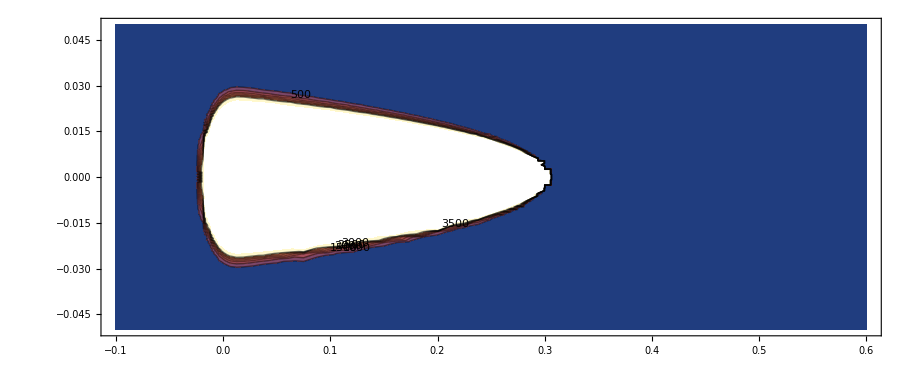

```mathematica
ContourPlot[θ[50,ρ,kappa,x,y,0.0,10,B,d,l,a,b,c,0.03],{x,-10 10^-2,60 10^-2},{y,-5 10^-2,5 10^-2},ContourLabels->True, AspectRatio->True]
```

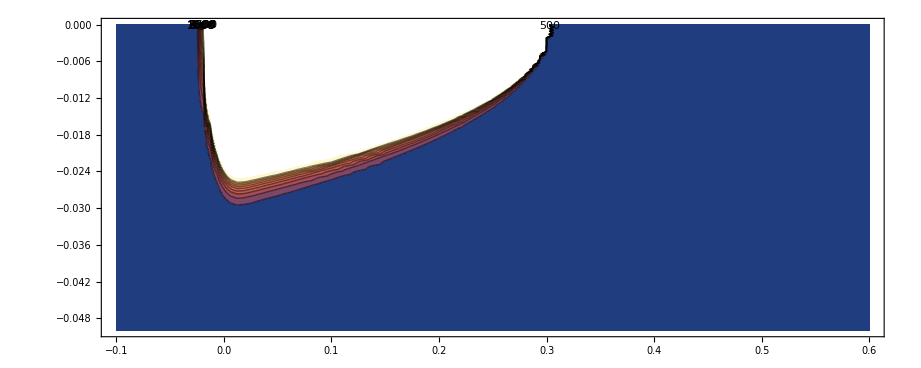

```mathematica
ContourPlot[θ[50,ρ,kappa,x,0.0,z,10,B,d,l,a,b,c,0.03],{x,-10 10^-2,60 10^-2},{z,0 10^-2,-5 10^-2},ContourLabels->True, AspectRatio->True]
```

We are plotting the temperature distribution in the middle of the scanning vector:

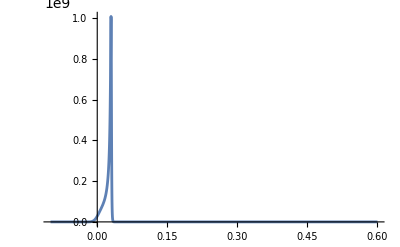

```mathematica
Plot[θ[50,ρ,kappa,x,0.0,0.001,10.0,B,d,l,a,b,c,0.003],{x,-10 10^-2,60 10^-2}, PlotRange->All]
```

Circular disk equation as special case of the elliptical heat source:

```mathematica
θcirc[Q_,κ_,σ_,x_,y_,z_,t_,v_]:= Q/(π ρ cp)NIntegrate[1/(Sqrt[4π κ(t-ts)](4κ(t-ts)+2 σ^2))Exp[- ((x-v ts)^2+y^2)/(4 κ(t-ts)+2 σ^2)-z^2/(4 κ(t-ts))],{ts,0,t}]
```

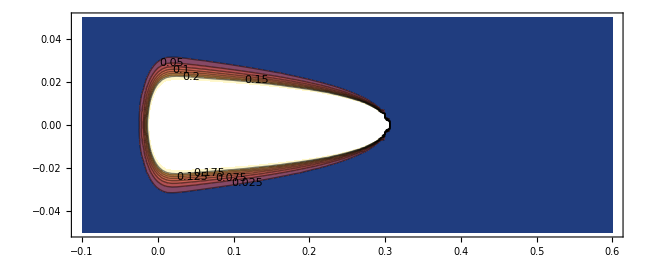

```mathematica
ContourPlot[θcirc[100,29/(7820*600),a/√6,x,y,0.0,10,0.03],{x,-10 10^-2,60 10^-2},{y,-5 10^-2,5 10^-2},ContourLabels->True, AspectRatio->True]
```

```mathematica
Plot3D[θcirc[100,29/(7820*600),a/√6,x,y,0.0,10,0.02],{x,-10 10^-2,60 10^-2},{y,-5 10^-2,5 10^-2},AspectRatio->True]
```

-Graphics3D-

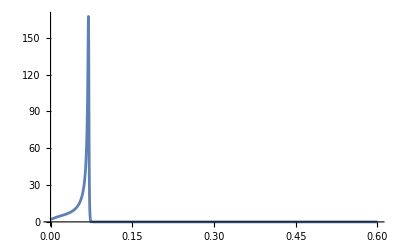

```mathematica
Plot[θcirc[50,29/(7820*600),a/√6,x,0.001,0.0,10,0.007],{x,0.,60 10^-2},  PlotRange->All]
```

Do the oscillation of the power input variable:
P(t) = P*sin(ω t)

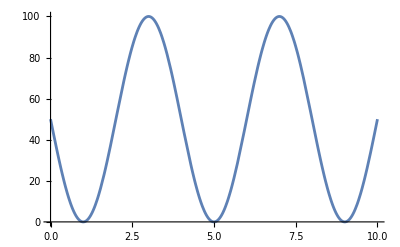

```mathematica
k =4; ω =2 π; 𝒫=50;
P[t_]:= 𝒫*(1-Sin[ω/k t]);
sh01=Plot[P[t], {t,0,10}]
```

```mathematica
maxtemperature = Table[Max[Table[θcirc[P[t],29/(7820*600),a/√6,x,0.001,0.0,10,0.007],{x,0.,60 10^-2,0.001}]],{t,0,10,0.1}];
```

General::munfl: 6.55039×10^-6 3.64267×10^-304 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.55039×10^-6 1.2261×10^-305 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.55039×10^-6 4.09378×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ts near {ts} = {0.0806395}. NIntegrate obtained 4.78726×10^-316 and 5.524×10^-321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ts near {ts} = {0.131322}. NIntegrate obtained 1.50884×10^-317 and 2.94×10^-321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ts near {ts} = {0.0624494}. NIntegrate obtained 4.5184×10^-319 and 1.863×10^-321 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

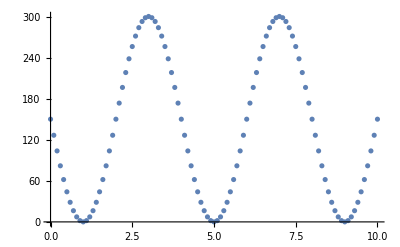

```mathematica
sh02=ListPlot[ Partition[Riffle[Table[0.1*t,{t,0,100}],maxtemperature],2]]
```

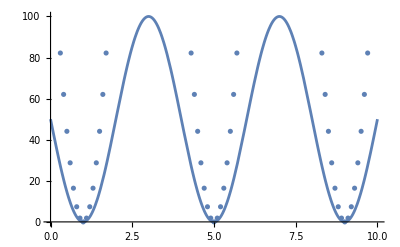

```mathematica
Show[{sh01,sh02}]
```